```mathematica
Aphi=R
BR=D[Aphi,h]/R
BRhat=BR*Sqrt[1]
BH=-D[Aphi,R]/R
BHhat=BH*R
bsq=BRhat^2+BHhat^2
```

R

0

0

-1/R

-1

1

```mathematica
bsq//.{h->0}
```

1

```mathematica
gcov
```

{{-1+(2 M x)/(x^2+a^2 Cos[y]^2),(2 M x)/(x^2+a^2 Cos[y]^2),0,-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)},{(2 M x)/(x^2+a^2 Cos[y]^2),1+(2 M x)/(x^2+a^2 Cos[y]^2),0,-a (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2},{0,0,x^2+a^2 Cos[y]^2,0},{-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2),-a (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2,0,Sin[y]^2 (x^2+a^2 Cos[y]^2+a^2 (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2)}}

```mathematica
tcon={1,0,0,0}
phicon={0,0,0,1}
tcov=tcon.gcov
phicov=phicon.gcov
```

{1,0,0,0}

{0,0,0,1}

{-1+(2 M x)/(x^2+a^2 Cos[y]^2),(2 M x)/(x^2+a^2 Cos[y]^2),0,-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)}

{-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2),-a (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2,0,Sin[y]^2 (x^2+a^2 Cos[y]^2+a^2 (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2)}

```mathematica
Acov=B0*(tcov*2*a+phicov)
```

{B0 (2 a (-1+(2 M x)/(x^2+a^2 Cos[y]^2))-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)),B0 ((4 a M x)/(x^2+a^2 Cos[y]^2)-a (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2),0,B0 (-(4 a^2 M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)+Sin[y]^2 (x^2+a^2 Cos[y]^2+a^2 (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2))}

```mathematica
Xp
```

{t,x,y,z}

```mathematica
gdet
```

(x^2+a^2 Cos[y]^2) Sin[y]

```mathematica
Fcov=Table[MyD[Acov[[mu]],nu]-MyD[Acov[[nu]],mu],{mu,1,4},{nu,1,4}];
Fcon=gcon.(Fcov.gcon);
Mcon=Table[Sum[1/2*(-1/gdet)*Signature[{a,b,c,d}]*Fcov[[c,d]],{c,1,4},{d,1,4}],{a,1,4},{b,1,4}];
Mcov=gcov.(Mcon.gcov);
```

```mathematica
Ephi=FullSimplify[Fcov[[1,4]],{M>0,a>0,B0>0,y≥0,x>0}]
```

0

```mathematica
Jcon=1/gdet*Table[Sum[MyD[gdet*Fcon[[mu,nu]],nu],{nu,1,4}],{mu,1,4}];
FullSimplify[Jcon,{M>0,a>0,B0>0,y≥0,x>0}]
```

{0,0,0,0}

```mathematica
Ecov=Table[Fcov[[ii,1]]/gdet,{ii,1,4}];
Econ=Table[Fcon[[1,ii]]*gdet,{ii,1,4}];
```

```mathematica
Bcov=Table[Mcov[[1,i]],{i,1,4}];
Bcon=Table[Mcon[[i,1]],{i,1,4}];
(*OmegaF=FullSimplify[Ecov[[3]]/Bcon[[2]],{M>0,a>0,B0>0,y≥0,x>0}];*)
OmegaF=FullSimplify[Fcov[[1,3]]/Fcov[[3,4]],{M>0,a>0,B0>0,y≥0,x>0}];
EdotB=(1/4)*Sum[Fcov[[mu,nu]]*Mcon[[mu,nu]],{mu,1,4},{nu,1,4}];
bsq=(1/2)*Sum[Fcov[[mu,nu]]*Fcon[[mu,nu]],{mu,1,4},{nu,1,4}];
```

```mathematica
(*set omegaf1=fdd01/fdd13 #=ftr/frp
set omegaf2=fdd02/fdd23*)
```

```mathematica
FullSimplify[Bcov[[4]],{M>0,a>0,B0>0,y≥0,x>0}]
```

$Aborted

```mathematica
FullSimplify[Bcov[[4]]//.{M->1.,a->1/2,B0->1,y->Pi/4,x->3}]
```

-0.232052

-(3.24 x Sin[y]^2)/(x^2+0.81 Cos[y]^2)+Sin[y]^2 (x^2+0.81 Cos[y]^2+0.81 (1+(2 x)/(x^2+0.81 Cos[y]^2)) Sin[y]^2)

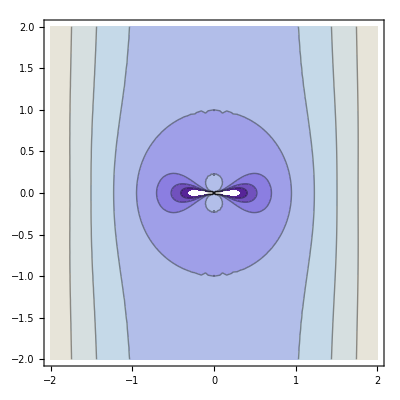

```mathematica
fun=Acov[[4]]//.{B0->1,M->1,a->0.9}
funtoplot=fun//.{x->Sqrt[xx^2+yy^2],y->ArcTan[xx/yy]};
ContourPlot[funtoplot,{xx,-2,2},{yy,-2,2}]
```

(14.4 x (-0.81+x^2))/(1.59432+7.2171 (-2+x) x+12.96 (-1+x) x^3+8 x^6+0.81 (0.81+(-2+x) x) (4 (0.81+2 x^2) Cos[2 y]+0.81 Cos[4 y]))

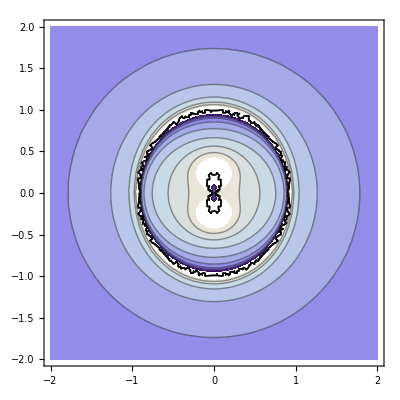

```mathematica
fun=OmegaF//.{B0->1,M->1,a->0.9}
funtoplot=fun//.{x->Sqrt[xx^2+yy^2],y->ArcTan[xx/yy]};
ContourPlot[funtoplot,{xx,-2,2},{yy,-2,2}]
```

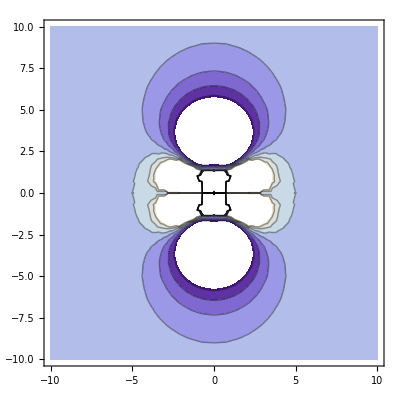

```mathematica
fun=Bcov[[1]]//.{B0->1,M->1,a->0.9};
funtoplot=fun//.{x->Sqrt[xx^2+yy^2],y->ArcTan[xx/yy]};
ContourPlot[funtoplot,{xx,-10,10},{yy,-10,10}]
```

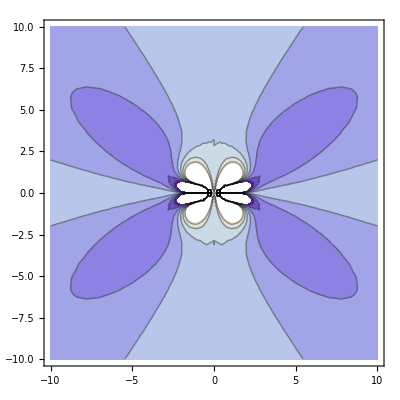

```mathematica
fun=Bcov[[4]]//.{B0->1,M->1,a->0.9};
funtoplot=fun//.{x->Sqrt[xx^2+yy^2],y->ArcTan[xx/yy]};
ContourPlot[funtoplot,{xx,-10,10},{yy,-10,10}]
```

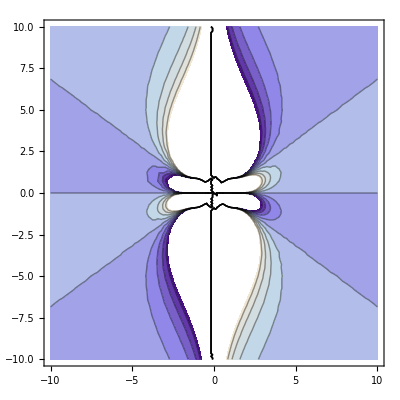

```mathematica
fun=Ecov.Bcon//.{B0->1,M->1,a->0.9};
funtoplot=fun//.{x->Sqrt[xx^2+yy^2],y->ArcTan[xx/yy]};
ContourPlot[funtoplot,{xx,-10,10},{yy,-10,10}]
```

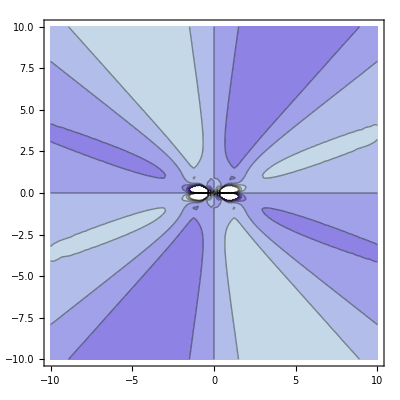

```mathematica
fun=Econ.Bcov//.{B0->1,M->1,a->0.9};
funtoplot=fun//.{x->Sqrt[xx^2+yy^2],y->ArcTan[xx/yy]};
ContourPlot[funtoplot,{xx,-10,10},{yy,-10,10}]
```

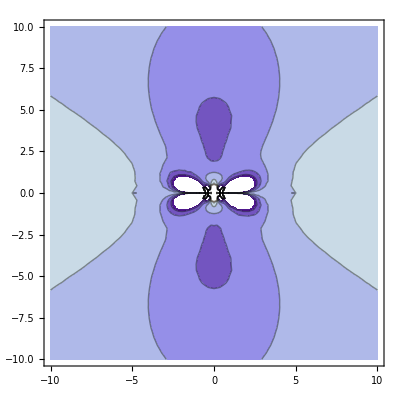

```mathematica
fun=EdotB//.{B0->1,M->1,a->0.9};
funtoplot=fun//.{x->Sqrt[xx^2+yy^2],y->ArcTan[xx/yy]};
ContourPlot[funtoplot,{xx,-10,10},{yy,-10,10}]
```

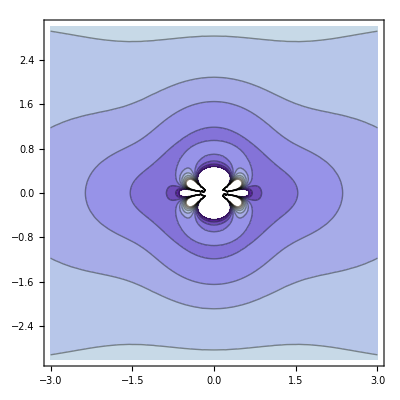

```mathematica
fun=bsq//.{B0->1,M->1,a->0.9};
funtoplot=fun//.{x->Sqrt[xx^2+yy^2],y->ArcTan[xx/yy]};
ContourPlot[funtoplot,{xx,-3,3},{yy,-3,3}]
```

```mathematica
(*S=ExB*)
```

```mathematica
T=Table[Fcov[[mu,lambda]]*gcov[[]]*Fcon[[nu,lambda]]*gcov[[
```